# Evaluating Genetic-Based Disease Prediction Approaches Through Simulation

## Code

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/ROCFunctions.m"]
```

```mathematica
Needs["RLink`"]
```

```mathematica
InstallR["RHomeLocation"->"D:/Program Files/R/R-3.6.0"]
```

```mathematica
(*REvaluate["install.packages(c(\"glmnet\",\"MASS\")"]*)
```

```mathematica
REvaluate["{library(glmnet);library(MASS)}"]
```

{MASS,glmnet,Matrix,stats,graphics,grDevices,utils,datasets,methods,base}

```mathematica
realQ[x_]:=!ListQ[x]&&Element[x,Reals]
```

```mathematica
fractionalQ[x_]:=realQ[x]&&0≤x≤1
```

```mathematica
pDisease[f11_?fractionalQ,f12_?fractionalQ,f22_?fractionalQ,pA1_?fractionalQ]:=
f11 pA1^2+f12 2pA1(1-pA1)+f22(1-pA1)^2
```

```mathematica
pAllelesGivenDisease[f11_?fractionalQ,f12_?fractionalQ,f22_?fractionalQ,pA1_?fractionalQ]:=
{f11 pA1^2/#,(f11 pA1^2+f12 2 pA1(1-pA1))/#}&[
pDisease[f11,f12,f22,pA1]]
```

```mathematica
pAllelesGivenControl[f11_?fractionalQ,f12_?fractionalQ,f22_?fractionalQ,pA1_?fractionalQ]:=
With[{myPDisease=pDisease[f11,f12,f22,pA1]},
(#1-#2 myPDisease)/(1-myPDisease)&@@@
Transpose[{{pA1^2,pA1^2+2pA1(1-pA1)},
pAllelesGivenDisease[f11,f12,f22,pA1]}]]
```

```mathematica
genotypes[genotypeNum_Integer,recessivesMax_?fractionalQ,dominantsMin_?fractionalQ]:=
Replace[{_?(#<recessivesMax&):>1,_?(dominantsMin<#&):>3,_:>2}]/@
RandomReal[{0,1},genotypeNum]
```

```mathematica
genotypesSim[genotypeNum_Integer,f1_?fractionalQ,f12_?fractionalQ,f22_?fractionalQ,pA1_?fractionalQ,type:"control"|"disease"]:=
genotypes[genotypeNum,##]&@@
Replace[type,{"control"->pAllelesGivenControl,"disease"->pAllelesGivenDisease}][
f1,f12,f22,pA1]
```

```mathematica
genomesSimPart[f11_?fractionalQ,f12_?fractionalQ,f22_?fractionalQ,pA1s:{___?fractionalQ},genomeNum_Integer,type:"control"|"disease"]:=
Transpose[genotypesSim[genomeNum,f11,f12,f22,#,type]&/@
pA1s]
```

```mathematica
genomesSim[f11_?fractionalQ,f12_?fractionalQ,f22_?fractionalQ,diseasePA1s:{___?fractionalQ},nullPA1s:{___?fractionalQ},permutation:{___Integer},genomeNum_Integer,type:"control"|"disease"]:=
Permute[#,permutation]&/@
Join[
genomesSimPart[f11,f12,f22,diseasePA1s,genomeNum,type],
genomesSimPart[.5,.5,.5,nullPA1s,genomeNum,type],
2]/;
Length[permutation]==Length[Join[diseasePA1s,nullPA1s]]
```

```mathematica
aUCSFromValues[modelValues:{___?realQ}/;EvenQ[Length[modelValues]]]:=
ROCFunctions["AUROC"][
(x↦
ToROCAssociation[
{0,1}, 
Join[ConstantArray[0,Length[modelValues]/2],ConstantArray[1,Length[modelValues]/2]],
If[# > x, 1, 0] &/@
modelValues])/@
Union[modelValues]]
```

```mathematica
lassoFeatures[data:{(_->_)...},lambdas:{__?realQ}]:=
(RSet["x",First/@data];
RSet["y",Last/@data];
RSet["lambdas",lambdas];
Catenate[Position[#,1,1]]&/@(Transpose[
REvaluate["as.array(coef(glmnet(x, y, family = \"binomial\", alpha = 1, lambda = lambdas)))"][[1,2;;]]]/.
{0.->0,_?realQ->1}))
```

```mathematica
reverseFeatures[data:{(_->_)...}]:=
ToExpression[StringTake[
With[{splitTests=({First/@#[0],First/@#[1]}&[GroupBy[data,Last]])},
RSet["control",First[splitTests]];
RSet["case",Last[splitTests]]];
REvaluate["{
		control <- as.data.frame(control)
		case <- as.data.frame(case)
		control$y <- 0
		case$y <- 1
		data1 <- rbind(case,control)
		data1$y <- factor(data1$y)
		full.model <- glm(y~.,data = data1,family = binomial)
		step_model <- stepAIC(full.model, trace = T,direction = \"backward\")
		n <- names(step_model$coefficients)
		as.array(n[-1])
	}"]
,{2,-1}]]
```

```mathematica
myPredict[trainings_List, tests_List,  Method -> method_String] :=
 If[StringMatchQ[method, "NaiveBayes"|"LogisticRegression"], #[1] & /@
 Classify[trainings,Method -> method,TargetDevice->"GPU"][tests, "Probabilities"],
# /@ tests &[
   Predict[trainings, Method->method,TargetDevice->"GPU"]]]
```

```mathematica
selectThenEvaluate[trainings_List,tests_List,features:{___Integer},predictor_,evaluator_]:=
evaluator[
predictor[
MapAt[
#[[features]]&,
trainings,
{All,1}],
tests[[All,features]]]]
```

```mathematica
lasso::lsmh="No lambdas selected. MinPercentage may be too high.";
```

```mathematica
lasso::nfs="No features selected. Perhaps lambdas are too low.";
```

```mathematica
lasso[trainings_List,tests_List,minPercentage_?fractionalQ,lambdas:{__?realQ},predictor_,evaluator_]:=
With[{features=
Select[lassoFeatures[trainings,lambdas],
Length[#]≥Ceiling[minPercentage Length[trainings]]&]},
If[features=={},
Message[lasso::lsmh],
With[{aUCs=selectThenEvaluate[trainings,tests,#,predictor,evaluator]&/@
features},
With[{maxIndex=First[Ordering[aUCs,-1]]},
If[Length[features[[maxIndex]]]==0,
Message[lasso::nfs];aUCs[[maxIndex]],
aUCs[[maxIndex]]]]]]]
```

```mathematica
genomeTestsGenerator[f11Init_?fractionalQ,diseaseAlpha_?realQ,diseaseBeta_?realQ,nullAlpha_?realQ,nullBeta_?realQ,diseaseSNPNum_Integer,nullSNPNum_Integer,trainingGenomeNum_Integer,testGenomeNum_Integer][inheritance_String][delta_?realQ][]:=
With[{
freqs=Switch[inheritance,
"additive",{f11Init+delta,f11Init+2delta},
"dominant",{f11Init+2delta,f11Init+2delta},
"recessive",{f11Init,f11Init+2delta}],
diseasePA1s=RandomVariate[BetaDistribution[diseaseAlpha,diseaseBeta],diseaseSNPNum],
nullPA1s=RandomVariate[BetaDistribution[nullAlpha,nullBeta],nullSNPNum],
permutation=RandomSample[Range[diseaseSNPNum+nullSNPNum]]},
<|"trainings"->
Join[
#->0&/@genomesSim[f11Init,Sequence@@freqs,diseasePA1s,nullPA1s,permutation,trainingGenomeNum,"control"],
#->1&/@genomesSim[f11Init,Sequence@@freqs,diseasePA1s,nullPA1s,permutation,trainingGenomeNum,"disease"]],
"tests"->Join[
genomesSim[f11Init,Sequence@@freqs,diseasePA1s,nullPA1s,permutation,testGenomeNum,"control"],
genomesSim[f11Init,Sequence@@freqs,diseasePA1s,nullPA1s,permutation,testGenomeNum,"disease"]]|>]
```

```mathematica
$applicateesP=<|(_String->{(_String->_)..})..|>;
```

```mathematica
generateMeanApply[generator_,applicator_,applicatees:$applicateesP,runs_Integer:1]:=
(valueTypes|->
Prepend["meanValue"->MeanAround[Lookup["value"]/@valueTypes]][
KeyDrop[First[valueTypes],"value"]])/@
Transpose[ResourceFunction["MonitorProgress"][
Table[With[{generatee=generator[]},
ResourceFunction["MonitorProgress"][
<|"value"->applicator[generatee,Sequence@@Last/@#],
Sequence@@
MapThread[(#1->First[#2]&),
{Keys[applicatees],#}]|>&/@
Tuples[Values[applicatees]]]],
runs]]]
```

```mathematica
generateMeanApplyList[generator_,applicator_,applicatees:$applicateesP,{init_?realQ,final_?realQ,delta_?realQ},runs_Integer:1]:=
(valueTypes|->Prepend[KeyDrop[First[valueTypes],"meanValue"],"values"->(Lookup["meanValue"]/@valueTypes)])/@
Transpose[
ResourceFunction["MonitorProgress"][
Table[
generateMeanApply[generator[i],applicator,applicatees,runs],
{i,init,final,delta}]]]
```

```mathematica
plotter[{init_?realQ,final_?realQ,delta_?realQ},opts:OptionsPattern[ListLinePlot]][allAUCs:{___Association},grouper:"predictor"|"selector"]:=
Multicolumn[
KeyValueMap[
ListLinePlot[
Legended[
#["values"],
#[Replace[grouper,{"predictor"->"selector","selector"->"predictor"}]]]&/@
#2,
PlotLabel->#1,
DataRange->{init,final},
AxesOrigin->{init-delta,Automatic},
PlotRange->{0,1.05},
AxesLabel->{"Delta","Area Under ROC Curve"},opts]&,
GroupBy[allAUCs,Lookup[grouper]]],
Appearance->"Horizontal"]
```

```mathematica
noFeatureSelection[trainings_,tests_,predictor_,evaluator_]:=evaluator[predictor[trainings,tests]]
```

```mathematica
myApplicator[values_,predictor_,selector_,evaluator_]:=selector[values["trainings"],values["tests"],predictor,evaluator]
```

```mathematica
alpha=1.9195011886;beta=5.6066750138;
diseaseSNPNum=50;
nullSNPNum=25;
trainingGenomeNum=50;
testGenomeNum=50;
runs=6;
f11Init=.01;
delta=.025;
deltaFinal=.15;
minFeatures=.1;
lassoLambdas=N[Table[10^n,{n,-3,0}]];
```

```mathematica
myGenomeTestsGen=genomeTestsGenerator[f11Init,alpha,beta,alpha,beta,diseaseSNPNum,nullSNPNum,trainingGenomeNum,testGenomeNum];
```

```mathematica
myPredictorNames={"LogisticRegression","RandomForest","NaiveBayes","NeuralNetwork"};
```

```mathematica
myPredictors=(predictor|->ResourceFunction["FromCamelCase"][predictor]->(myPredict[#1,#2,Method->predictor]&))/@myPredictorNames
```

{Logistic Regression→(myPredict[#1,#2,Method→LogisticRegression]&),Random Forest→(myPredict[#1,#2,Method→RandomForest]&),Naive Bayes→(myPredict[#1,#2,Method→NaiveBayes]&),Neural Network→(myPredict[#1,#2,Method→NeuralNetwork]&)}

```mathematica
myApplicatees=<|
"predictor"->myPredictors,
"selector"->{
"No Feature Selection"->noFeatureSelection,
"LASSO"->(lasso[#1,#2,minFeatures,lassoLambdas,#3,#4]&),
"Reverse Selection"->(selectThenEvaluate[#1,#2,reverseFeatures[#1],#3,#4]&)},
"evaluator"->{"aUCs"->aUCSFromValues}|>;
```

```mathematica
diseaseAUCS[inheritance_String]:=generateMeanApplyList[myGenomeTestsGen[inheritance],myApplicator,myApplicatees,{0,deltaFinal,delta},runs]
```

```mathematica
myPlotter=plotter[{0,deltaFinal,delta},ImageSize->Large];
```

```mathematica
randomSeed=1;
```

```mathematica
SeedRandom[randomSeed];
```

```mathematica
RSet["randomSeed",randomSeed];
```

```mathematica
REvaluate["set.seed(randomSeed)"];
```

## Results

### Additive Inheritance

```mathematica
additiveAUCS=diseaseAUCS["additive"];
```

#### By Feature Selector

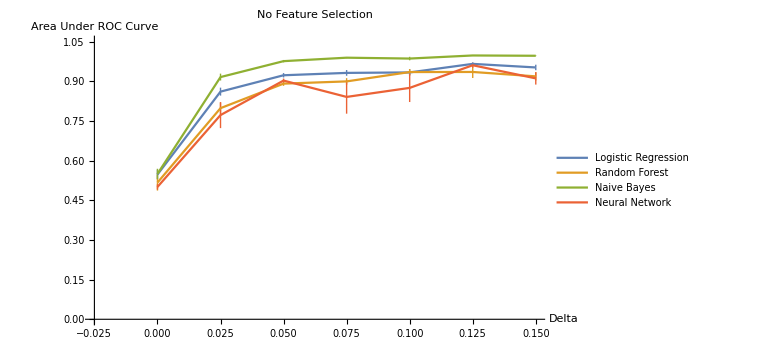
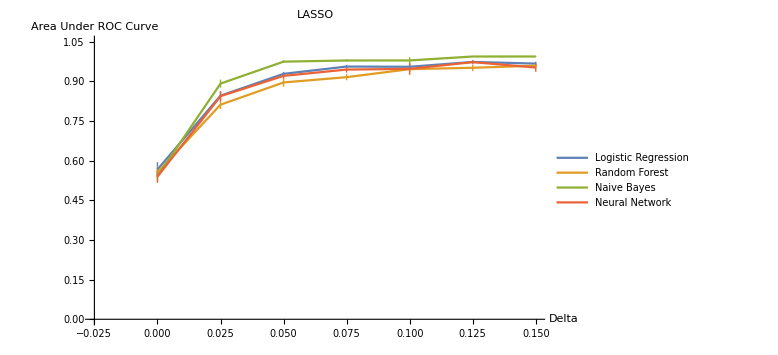
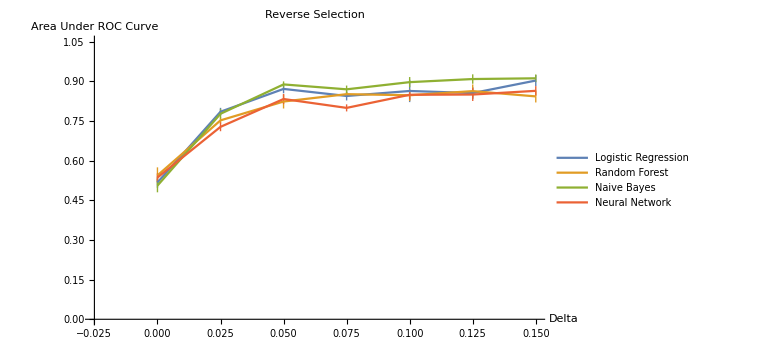
-Graphics- | -Graphics-
-Graphics- |

```mathematica
myPlotter[additiveAUCS,"selector"]
```

#### By Predictor

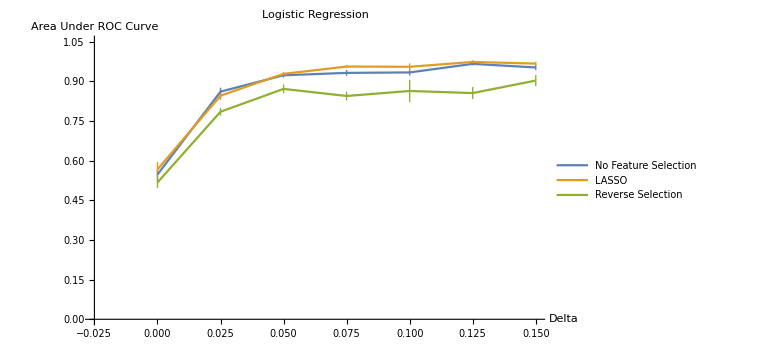
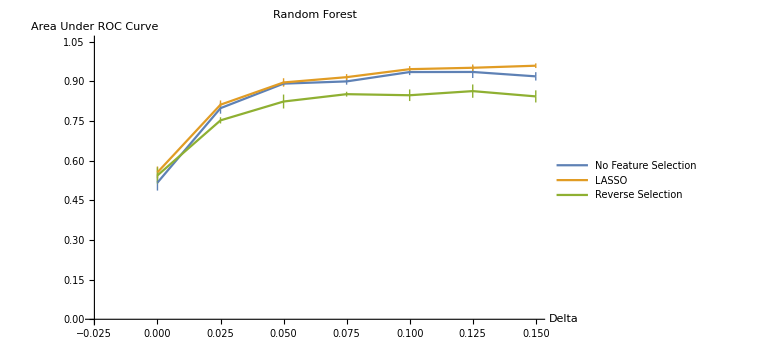
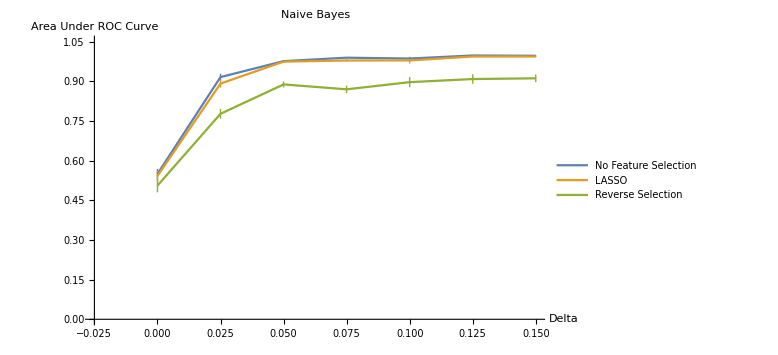
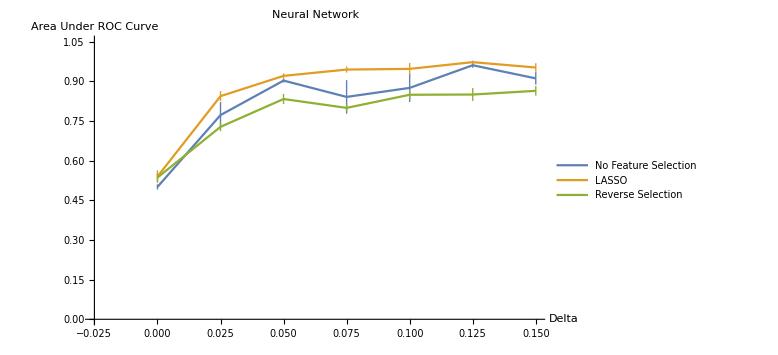
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
myPlotter[additiveAUCS,"predictor"]
```

### Dominant Inheritance

```mathematica
dominantAUCS=diseaseAUCS["dominant"];
```

#### By Feature Selector

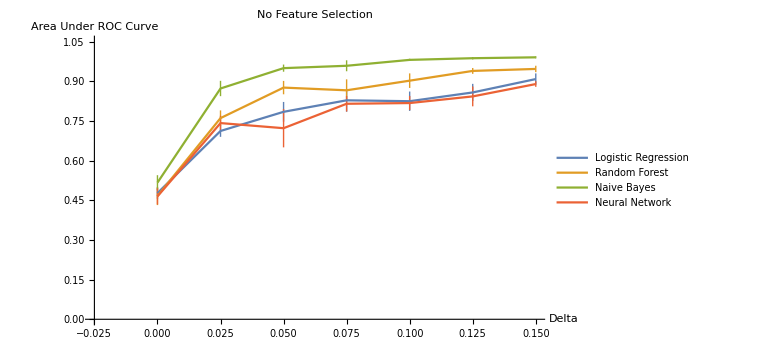
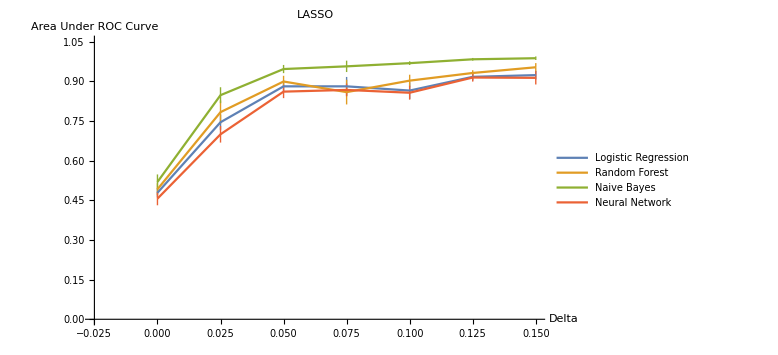
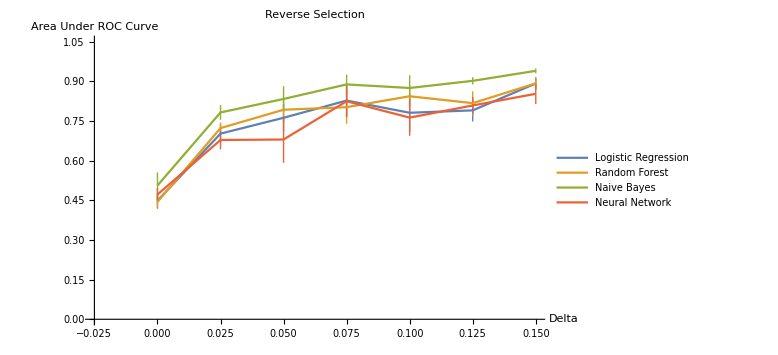
-Graphics- | -Graphics-
-Graphics- |

```mathematica
myPlotter[dominantAUCS,"selector"]
```

#### By Predictor

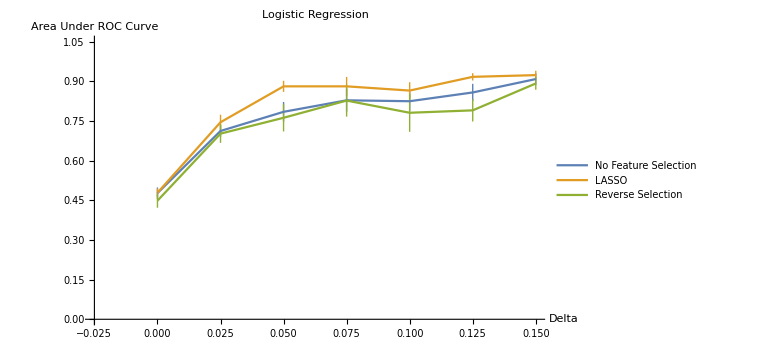
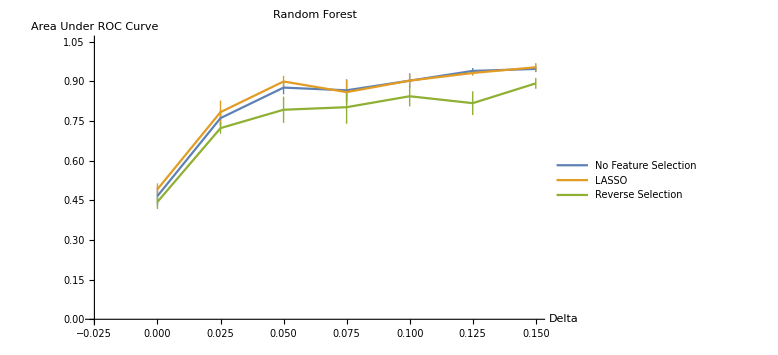
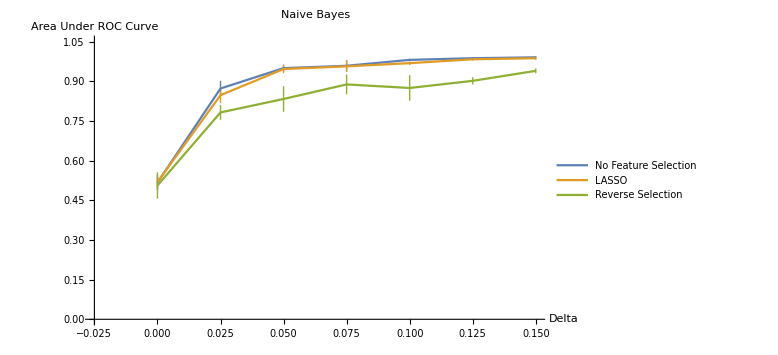
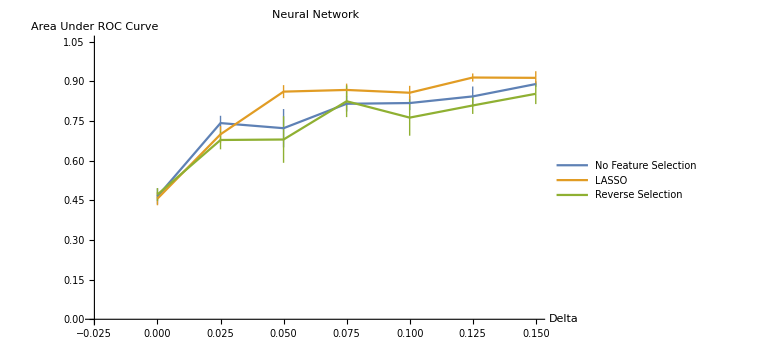
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
myPlotter[dominantAUCS,"predictor"]
```

### Recessive Inheritance

```mathematica
recessiveAUCS=diseaseAUCS["recessive"];
```

#### By Feature Selector

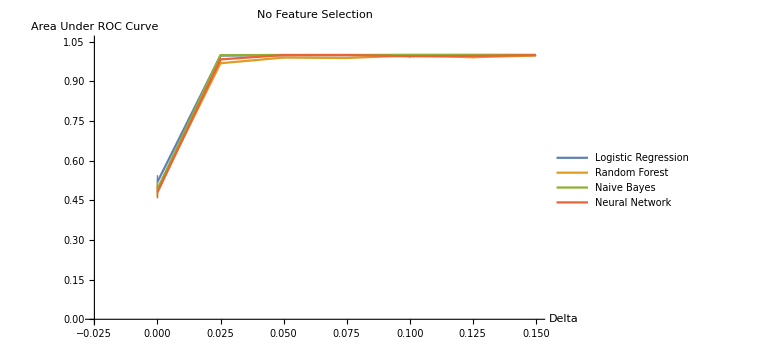
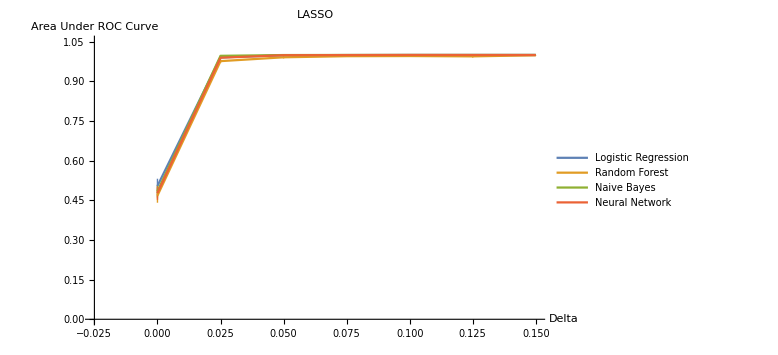
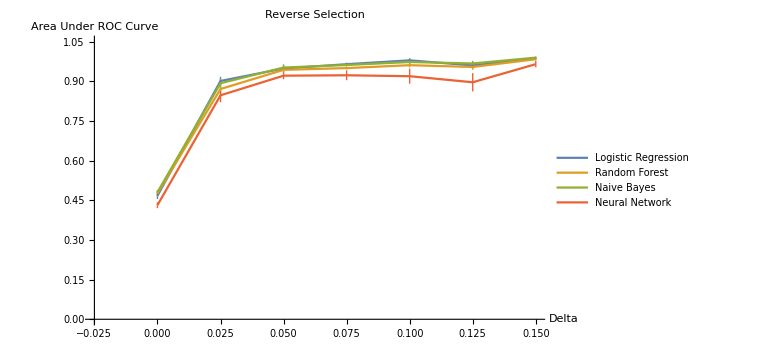
-Graphics- | -Graphics-
-Graphics- |

```mathematica
myPlotter[recessiveAUCS,"selector"]
```

#### By Predictor

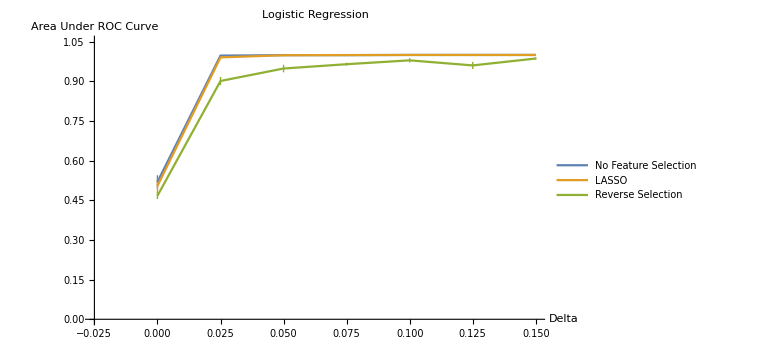
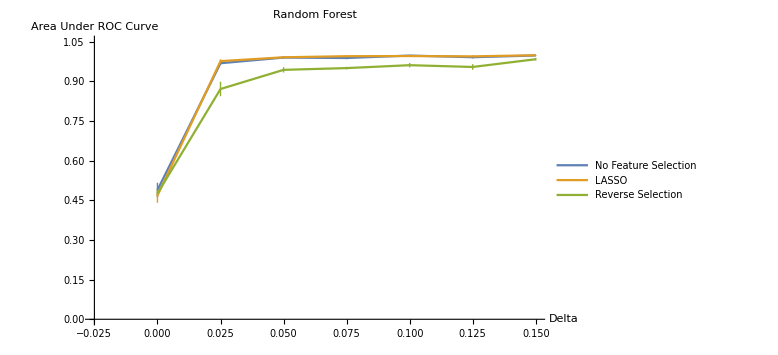
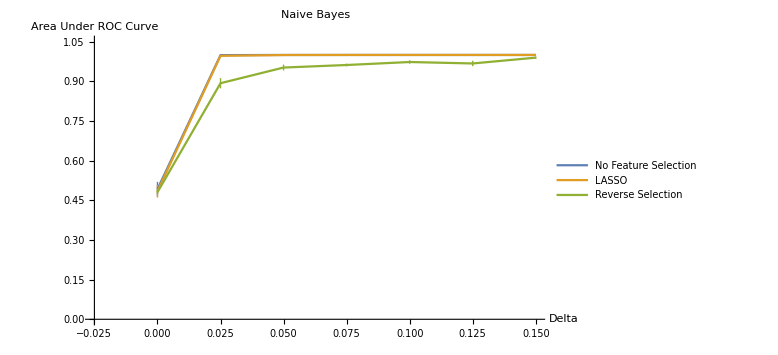
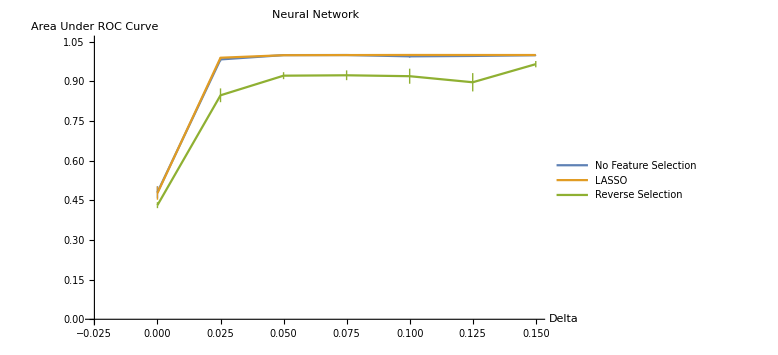
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
myPlotter[recessiveAUCS,"predictor"]
```